```mathematica
2 √3
```

2 √3

```mathematica
N[2 √3]
```

3.4641

```mathematica
RootApproximant[3.4641016151377544]
```

2 √3

```mathematica
(3 + 5 i) (4 + 65i)
```

(3+5 i) (4+65 i)

```mathematica
FullSimplify[(3+5 i) (4+65 i)]
```

```mathematica
(3+5 I) (4+65 I)
```

-313+215 ⅈ

```mathematica
Sqrt[-54]
```

3 ⅈ √6

```mathematica
x= 5^435-1;
```

```mathematica
x
```

```mathematica
1127072585178922824799674165343851738018629604499085941784946172656612572055800691265229320350631197480268759684274691255812893039253642292321402943534005460097232154008970480277910839758456787702979452339482651557826108230097152073523105683967777902902019950524565433669366143476509023457765579223632812
```

```mathematica
(1/2+1/3)^3
```

125/216

```mathematica
N[125/216]
```

0.578704

```mathematica
e^pi
```

e^pi

```mathematica
Plot3D[e^pi,{e,-8,8},{pi,-8,8}]
```

-Graphics3D-

```mathematica
y=e^pi;
```

```mathematica
y
```

e^pi

```mathematica
ⅇ^π
```

ⅇ^π

```mathematica
N[ⅇ^π]
```

23.1407

```mathematica
π^ⅇ
```

π^ⅇ

```mathematica
N[π^ⅇ]
```

22.4592

```mathematica
ⅇ^(π i + 1)
```

ⅇ^(1+i π)

```mathematica
FourierSequenceTransform[ⅇ^(1+i π),i,ω]
```

FourierSequenceTransform[ⅇ^(1+i π),i,ω]

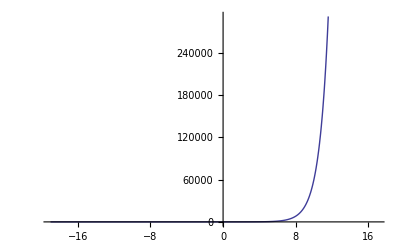

```mathematica
Plot[ⅇ^(1+πI),{πI,-19.,17.}]
```

```mathematica
Plot3D [ x^2 + y^2, {x, -2, 2}, {y, -2, 2}, 
BoxRatios-> Automatic->RegionFunction -> Function 
[{x, y, z}, x^2+ y^2 < 4]]
```

-Graphics3D-

```mathematica
Plot3D [ x^2, {x, -2, 2}, {y, -2, 2}, 
BoxRatios-> Automatic,
RegionFunction -> Function [{x, y, z}, x^2+ y^2 < 4], 
BoundaryStyle->{Red, Thickness[.01]},
Filling->Bottom,
FillingStyle->{Green, Opacity[.3]},
Mesh -> 8,
MeshShading->{{Black, None}, {None, Black}}
]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Cos[x], {x, 0, 2 π}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Cos[x], {x, 0, 2 π}, {∅, 0,π}, 
				Boxed->False, Axes->False ]
```

-Graphics3D-

```mathematica
Graphics3D[{
{Red,
Table [Sphere[{i,j,k}, .25], {i, -1, 1}, {j, -1, 1}, {k, -1, 1}]},
{Blue,
Table [Cylinder[{{i,j,k}, {i, j, k+1}}, .1], {i, -1, 1}, {j, -1, 1}, {k, -1, 0}]},
{Blue,
Table [Cylinder[{{i,j,k}, {i, j+1, k}}, .1], {i, -1, 1}, {j, -1, 0}, {k, -1, 1}]},
{Blue,
Table [Cylinder[{{i,j,k}, {i+1, j, k}}, .1], {i, -1, 0}, {j, -1, 1}, {k, -1, 1}]}
}]
```

-Graphics3D-

```mathematica
f[x_] :=Sin[x]/x
```

```mathematica
f[0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
f
```

f

```mathematica
N@Table[f[10^k], {k, 0.-5,-1}]
```

{1.,1.,1.,0.999983,0.998334}

```mathematica
N@Table[f[-10^k], {k, 0.-5,-1}]
```

{1.,1.,1.,0.999983,0.998334}

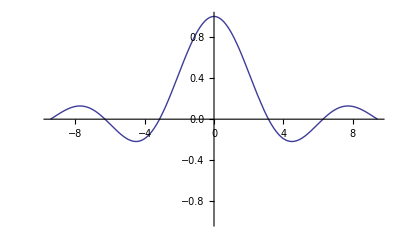

```mathematica
Plot[Sin[x]/x, {x, -3 Pi, 3 Pi},
PlotRange->{{-3 Pi, 3 Pi}, {-1, 1}}]
```

```mathematica
Limit[Sin[x]/x, x->0]
```

General::ivar: 11270725851789228247996741653438517380186296044990859417849461726566125720 « 157 » 35231056839677779029020199505245654336693661434765090234577655792236328124 is not a valid variable.

Limit[Sin[11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124]/11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124,11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124→0]

```mathematica
Limit[Sin[g]/g, g-> 0]
```

```mathematica
1
ClearAll
```

1

ClearAll

```mathematica
Limit[Sin[x]/x, x-> 0]
```

General::ivar: 11270725851789228247996741653438517380186296044990859417849461726566125720 « 157 » 35231056839677779029020199505245654336693661434765090234577655792236328124 is not a valid variable.

Limit[Sin[11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124]/11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124,11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124→0]

```mathematica
x
```

11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124

```mathematica
clear[x]
```

clear[11270725851789228247996741653438517380186296044990859417849461726566125720558006912652293203506311974802687596842746912558128930392536422923214029435340054600972321540089704802779108397584567877029794523394826515578261082300971520735231056839677779029020199505245654336693661434765090234577655792236328124]

```mathematica
Clear[x]
```

```mathematica
Limit[Sin[x]/x, x-> 0]
```

1

```mathematica
Limit[e^x/x, x-> Infinity]
```

Limit[e^x/x,x→∞]

```mathematica
Limit[e^x/x, x-> ∞]
```

Limit[e^x/x,x→∞]

```mathematica
x
```

x

```mathematica
Limit[(a x^2 + b)/(c x^2 + d x _ e), x -> Infinity]
```

a/c

```mathematica
Limit[(Sin[g]/g)^(1/g^2), g-> 0]
```

1/ⅇ^(1/6)

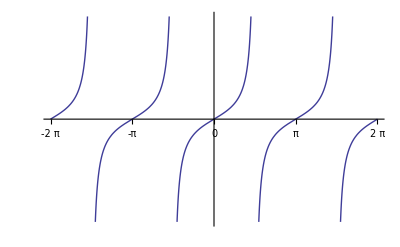

```mathematica
Plot[Tan[x], {x, -2 Pi, 2 Pi},
Ticks -> {Table[k Pi/2, {k, -4, 4}], None},
Exclusions -> Table[ j Pi/2, {j, -3, 3, 2}]
]
```

```mathematica
Limit[Tan[x], x-> Pi/2, Direction -> 1]
```

∞

```mathematica
Limit[Tan[x], x-> Pi/2, Direction -> -1]
```

-∞

```mathematica
Limit[Sin[1/x], x-> 0]
```

Interval[{-1,1}]